Андреєв М. В., ФКН, 3 курс, 4 варіант.

Тема 1. Введення в систему Mathematica.

#### Завдання 1. Арифметичні обчислення.

Обчислити значення арифметичного виразу

```mathematica
(0.012/5+ 0.04104/5.4)*4560 - (42+1/3)
```

3.26667

```mathematica
Rationalize[3.2666666666666657]
```

49/15

Завдання 2. Обчислення виразу з елементарними функціями.

Використовуючи систему «Mathematica», обчислити арифметичний
вираз.

```mathematica
y = Cot[5^(1/3)]- 1/8*Cos[4 √2]^2/Sin[8*Exp[2]];
```

```mathematica
N[y]
```

-0.290307

Тема 2. Алгебраїчні обчислення.

Завдання 1. Алгебраїчні перетворення.

Використовуючи систему «Mathematica», спростити вираз.

```mathematica
Remove[a,x]
```

```mathematica
Simplify[(2*a)/(a^2-4*x^2)+1/(2*x^2+6*x-a*x-3*a)*(x+(3*x-6)/(x - 2))]
```

1/(a+2 x)

Завдання 2. Обчислення значень алгебраїчних виразів.

Використовуючи систему «Mathematica», обчислити значення виразу при вказаних значеннях параметрів.

```mathematica
Remove[a,b]
```

```mathematica
Simplify[√(((1+a)*(1 + a)^(1/3))/(3*a))*((√3)/(9 + 18*a^-1+a^-2))^(1/3)/.{a->2}]
```

(3/73)^(1/3) 2^(1/6)

Завдання 3. Розв’язання рівнянь.

Використовуючи систему «Mathematica», розв’язати рівняння.

```mathematica
Remove[a, x]
Simplify[Solve[(c+3z)/(4 c^2 + 6c*d)- (c - 2z)/(9 d^2- 6c*d)==(2c+z)/(4 c^2-9 d^2), z]]
```

{{z→(4 c^3-9 c d^2)/(8 c^2+27 d^2)}}

Тема 3. Елементи аналітичної геометрії.

Завдання 1. Робота з векторами.

Використовуючи систему «Mathematica», з’ясувати, чи колінеарні вектори c1 і c2, які побудовані по векторам a та b. Знайти довжину векторів a і
b, та кут між ними. В системі Mathematica намалювати вектори a і b.

```mathematica
Remove[a, b, x]
```

```mathematica
a = {1, 2, -3};
b = {2, -1, -1};
c1 = 4a + 3b;
c2 = 8a - b;
c1/c2
```

{5/3,5/17,15/23}

```mathematica
Print["Не колінеарні"]
```

Не колінеарні

```mathematica
Norm[a]
```

√14

```mathematica
Norm[b]
```

√6

```mathematica
(N[VectorAngle[a, b]]*180)/π
```

70.8934

```mathematica
z = {0, 0, 0};
Graphics3D[{Thickness[0.02], Arrowheads[0.1], Arrow[{z, a}], Arrow[{z, b}]}, Axes->True, AxesLabel->{"X", "Y", "Z"}]
```

-Graphics3D-

Завдання 2. Геометричні обчислення в трикутнику.

Використовуючи систему «Mathematica», знайти довжини сторін,
величини кутів та площу трикутника з вершинами в точках A, B, C. Графічно зобразити досліджуваний трикутник.

```mathematica
Unprotect[C]
```

{C}

```mathematica
A = {1, -2, 3};
B = {3, 4, -6};
C = {1, 1, -1};
```

```mathematica
ListPlot3D[{A, B, C}, BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
AB = B - A
AC = C - A
BC = C - B
```

{2,6,-9}

{0,3,-4}

{-2,-3,5}

```mathematica
LAB = Norm[AB];
LAC = Norm[AC];
LBC = Norm[BC];
{LAB, LAC, LBC}
```

{11,5,√38}

```mathematica
aA = (N[VectorAngle[AB, AC]]*180)/π;
aB =(N[VectorAngle[-AB, BC]]*180)/π;
aC = (N[VectorAngle[AC, BC]]*180)/π;
{aA, aB, aC}
```

{10.9425,8.85691,160.201}

```mathematica
S = 1/2 Norm[Cross[AB, AC]]
```

(√109)/2

Завдання 3. Геометричні обчислення в тетраедрі.

Використовуючи систему «Mathematica», обчислити об’єм тетраедра з вершинами в точках A,B,C,D, та його висоту, яка випущена з
вершини D на грань ABC. Графічно зобразити тетраедр, його висоту і точку перетину висоти і основи тетраедра. Позначати вершини тетраедра можна будь - якими літерами, наприклад, A,B,C,D або A1,A2,A3,A4.

```mathematica
Unprotect[C, D, E];
```

```mathematica
A = {2, 1, 4};
B = {-1, 5, -2};
C = {-7, -3, 2};
D = {-6, 3, 6};
```

```mathematica
p1 = Graphics3D[{Thickness[0.02], Line[{A, B, C, A, D, B, C, D}]}, AxesLabel->{"X", "Y", "Z"}, Axes->True]
```

-Graphics3D-

```mathematica
AB = B - A;
AC = C - A;
AD = D - A;
V = 1/6 Abs[Det[{AB, AC, AD}]]
```

224/3

```mathematica
n = Cross[AB, AC];
S = 1/2 Norm[n]
```

8 √22

```mathematica
hh = Solve[1/3 S*h==V, h]
```

{{h→14 √(2/11)}}

```mathematica
h = hh[[1,1,2]];
E = D - n/Norm[n]*h;
p2 = ListPointPlot3D[{E}, PlotStyle->{Directive[PointSize[0.06], Red]}];
p3 = Graphics3D[{Thickness[0.02], Line[{D, E}]}];
Show[p1, p2, p3]
```

-Graphics3D-

Тема 4. Матричне числення.

Завдання 1. Робота з матрицями.

Використовуючи систему «Mathematica», знайти значення матричного многочлена 2A^2+3a+5E, якщо E одинична матриця. Знайти обернену матрицю  A ^-1. Обчислити визначник матриці A. Обчислити суму та різницю матриць A і B. Обчислити матричний 𝑨. 𝑩 та поелементний добуток 𝑨 ∗ 𝑩 матриць, обчислити різницю між цими добутками. Розв’язати матричне рівняння A X = B відносно матриці X.

```mathematica
A = {{1,2,0},{3,0,-1},{2,1,-1}};
M=2*A.A+3*A+5*IdentityMatrix[3];
M//MatrixForm
```

(22 | 10 | -4
11 | 15 | -1
12 | 9 | 2)

```mathematica
A1 = Inverse[A]
```

{{1/3,2/3,-2/3},{1/3,-1/3,1/3},{1,1,-2}}

```mathematica
MatrixForm[A1]
```

(1/3 | 2/3 | -2/3
1/3 | -1/3 | 1/3
1 | 1 | -2)

```mathematica
Det[A]
```

3

```mathematica
B = {{2,0,1},{3,0,2},{-1,1,2}};
A+B//MatrixForm
```

(3 | 2 | 1
6 | 0 | 1
1 | 2 | 1)

```mathematica
A-B//MatrixForm
```

(-1 | 2 | -1
0 | 0 | -3
3 | 0 | -3)

```mathematica
A.B//MatrixForm
```

(8 | 0 | 5
7 | -1 | 1
8 | -1 | 2)

```mathematica
A*B//MatrixForm
```

(2 | 0 | 0
9 | 0 | -2
-2 | 1 | -2)

```mathematica
A.B-A*B//MatrixForm
```

(6 | 0 | 5
-2 | -1 | 3
10 | -2 | 4)

```mathematica
X=A1.B//MatrixForm
```

(15/16 | 15/16 | -3/16
1/4 | 1/4 | -1/4
1/8 | 9/8 | 3/8)

Завдання 2. Робота з матрицями і векторами.

Дано вектор x та матриці A і B. Використовуючи систему «Mathematica», обчислити вектор y, який заданий матричним виразом, а також
вектор 𝑨 𝑩 − 𝑩 𝑨 𝒙. Розв’язати рівняння Au=x за допомогою оберненої матриці та правила Крамера. Для кожного стовпця і рядка матриці А знайти
суму елементів. Знайти максимальний і мінімальний елементи матриці В.

```mathematica
x = {-6,-2,3};
A = {{1,2,0},{3,0,-1},{2,1,-1}};
B = {{2,0,1},{3,0,2},{-1,1,2}};
```

```mathematica
y = (B.B.B.B+A.B).x
```

{4,36,39}

```mathematica
(A.B-B.A).x
```

{4,27,5}

```mathematica
u = Inverse[A].x
```

{-16/3,-1/3,-14}

Метод Крамера

```mathematica
A1 = Join[Transpose[{x}], A[[All,2;;3]],2];
A1//MatrixForm
```

(-6 | 2 | 0
-2 | 0 | -1
3 | 1 | -1)

```mathematica
A2 = Join[A[[All,1;;1]],Transpose[{x}], A[[All,3;;3]],2];
A2//MatrixForm
```

(1 | -6 | 0
3 | -2 | -1
2 | 3 | -1)

```mathematica
A3 = Join[A[[All,1;;2]],Transpose[{x}],2];
A3//MatrixForm
```

(1 | 2 | -6
3 | 0 | -2
2 | 1 | 3)

```mathematica
{x, y, z} = {Det[A1], Det[A2], Det[A3]}/Det[A]
```

{-16/3,-1/3,-14}

```mathematica
Total[A,{1}]
```

{6,3,-2}

```mathematica
Total[A, {2}]
```

{3,2,2}

```mathematica
Max[B]
```

3

Завдання 3. Створення матриць.

Самостійно знайдіть в довідковій системі потрібні функції роботи зі списками/масивами і розв’яжіть наступні задачі.

#### Задача 1.

Згенеруйте одновимірний масив з 16 випадкових дійсних чисел. Відсортуйте його за спаданням і перетворіть на матрицю A розміром 4 x 4.
Створіть матрицю B розміром 4 x 4 складену з одних п’ятірок. Згенеруйте матрицю C розміром 4 x 4, елементи якої Cij обчислюються за формулою Cij=i^2-j^2. Згенеруйте діагональний масив D з елементами на діагоналі [1,-1,2,-2]. Обчисліть масив A+ B -C - D + E-3 , де E одинична матриця розміром 4 x 4.

```mathematica
A = ArrayReshape[Sort[RandomReal[1000, {16}], Greater], {4,4}];
A//MatrixForm
```

(982.739 | 851.253 | 849.315 | 710.999
608.545 | 594.415 | 449.086 | 392.225
304.103 | 289.059 | 269.931 | 268.201
257.801 | 248.681 | 156.689 | 14.7093)

```mathematica
B = ArrayReshape[Table[5,16], {4, 4}];
```

```mathematica
B//MatrixForm
```

(5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5)

```mathematica
({{5, 5, 5, 5}, {5, 5, 5, 5}, {5, 5, 5, 5}, {5, 5, 5, 5}})
```

{{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5}}

```mathematica
Unprotect[C, D]
```

{}

```mathematica
C =Table[i^2-j^2, {i, 4}, {j, 4}];
C//MatrixForm
```

(0 | -3 | -8 | -15
3 | 0 | -5 | -12
8 | 5 | 0 | -7
15 | 12 | 7 | 0)

```mathematica
D = DiagonalMatrix[{1, -1, 2, -2}];
D//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | -2)

```mathematica
A+B-C-D+IdentityMatrix[4]-3//MatrixForm
```

(984.739 | 856.253 | 859.315 | 727.999
607.545 | 598.415 | 456.086 | 406.225
298.103 | 286.059 | 270.931 | 277.201
244.801 | 238.681 | 151.689 | 19.7093)

Задача 2.

Створіть матрицю Z елементи якої обчислюються за формулою Zij= Xi^2 -Yj^2, де X =[-3, 0,1, 2, 5], Y =[-5, 0 -4,1, 3] одновимірні масиви. Додайте до Z стовпець, складений з натуральних чисел 1,2,3,4,5. Потім між першим і другим рядками вставте рядок, складений з одиниць.

```mathematica
X = {-3,0,1,2,5};
Y={-5,0,-4,1,3};
```

```mathematica
Z = Insert[MapThread[Append,{Table[X[[i]]^2-Y[[j]]^2, {i,5}, {j,5}],{1,2,3,4,5}}],Table[1,6], 2];
Z//MatrixForm
```

(-16 | 9 | -7 | 8 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1
-25 | 0 | -16 | -1 | -9 | 2
-24 | 1 | -15 | 0 | -8 | 3
-21 | 4 | -12 | 3 | -5 | 4
0 | 25 | 9 | 24 | 16 | 5)

Задача 3.

Створити масив A розміром 5 x 5, у якого на головній діагоналі розташовані натуральні числа від 1 до 5, на верхній побічній діагоналі – одиниці, на нижній побічній – мінус одиниці, а інші елементи дорівнюють нулю. Створити масив В розміром 5 x 5 , всі рядки якого співпадають з вектором 5,4,3,2,1. Створити масив С розміром 5 x 5 , всі стовпці якого співпадають з вектором 2,4,6,8,10. Скласти всі масиви D=A+B+C. В масиві D замінити другий рядок одиницями, видалити останній стовпець та дописати праворуч до отриманого масиву масив з нулів розміром 5 x 2. В отриманому масиві замінити елементи, індекси яких одночасно задовольняють нерівностям 1 ≤ i ≤ 3, 3 ≤ j ≤ 5 , на трійки.

```mathematica
Unprotect[C,D]
```

{}

```mathematica
A1 = DiagonalMatrix[RandomInteger[{1,5},5]];
```

```mathematica
A2= Transpose@(Reverse/@DiagonalMatrix[Table[1,4],1]);
```

```mathematica
A3 = Transpose@(Reverse/@DiagonalMatrix[Table[-1,4],-1]);
```

```mathematica
A = A2+A3+A1;
A//MatrixForm
```

(3 | 0 | 0 | 1 | 0
0 | 3 | 1 | 0 | -1
0 | 1 | 5 | -1 | 0
1 | 0 | -1 | 4 | 0
0 | -1 | 0 | 0 | 4)

```mathematica
B = ConstantArray[{5,4,3,2,1},5];
B//MatrixForm
```

(5 | 4 | 3 | 2 | 1
5 | 4 | 3 | 2 | 1
5 | 4 | 3 | 2 | 1
5 | 4 | 3 | 2 | 1
5 | 4 | 3 | 2 | 1)

```mathematica
C = Transpose[ConstantArray[{2,4,6,8,10},5]];
C//MatrixForm
```

(2 | 2 | 2 | 2 | 2
4 | 4 | 4 | 4 | 4
6 | 6 | 6 | 6 | 6
8 | 8 | 8 | 8 | 8
10 | 10 | 10 | 10 | 10)

```mathematica
D=A+B+C;
D//MatrixForm
```

(10 | 6 | 5 | 5 | 3
9 | 11 | 8 | 6 | 4
11 | 11 | 14 | 7 | 7
14 | 12 | 10 | 14 | 9
15 | 13 | 13 | 12 | 15)

```mathematica
D = ReplacePart[D, 2->Table[1,5]];
```

```mathematica
D//MatrixForm
```

(10 | 6 | 5 | 5 | 3
1 | 1 | 1 | 1 | 1
11 | 11 | 14 | 7 | 7
14 | 12 | 10 | 14 | 9
15 | 13 | 13 | 12 | 15)

```mathematica
D =Transpose[Delete[Transpose[D], {5}]]
```

{{10,6,5,5},{1,1,1,1},{11,11,14,7},{14,12,10,14},{15,13,13,12}}

```mathematica
D//MatrixForm
```

(10 | 6 | 5 | 5
1 | 1 | 1 | 1
11 | 11 | 14 | 7
14 | 12 | 10 | 14
15 | 13 | 13 | 12)

```mathematica
D = Join[D, Table[0, 5,2],2];
D//MatrixForm
```

(10 | 6 | 5 | 5 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0
11 | 11 | 14 | 7 | 0 | 0
14 | 12 | 10 | 14 | 0 | 0
15 | 13 | 13 | 12 | 0 | 0)

```mathematica
D[[1;;3,3;;5]]=Table[3,{i,3},{j,3,5}];
D//MatrixForm
```

(10 | 6 | 3 | 3 | 3 | 0
1 | 1 | 3 | 3 | 3 | 0
11 | 11 | 3 | 3 | 3 | 0
14 | 12 | 10 | 14 | 0 | 0
15 | 13 | 13 | 12 | 0 | 0)

Задача 4.

Згенерувати матрицю випадкових цілих чисел з діапазону [-100,100] розміром 5 x 5. Поміняти місцями рядок, що містить максимальний елемент, з рядком, що містить мінімальний елемент. Якщо мінімальних (максимальних) елементів більш одного, то вибрати рядок з більшим індексом. Побудувати вектор, елементи якого є максимумами елементів всіх діагоналей, що паралельні головній.

```mathematica
A = RandomInteger[{-100,100},{5,5}];
A//MatrixForm
```

(62 | -78 | 62 | 71 | 12
-60 | 9 | 86 | -93 | -98
92 | -10 | 76 | -20 | 95
-75 | -24 | -51 | 20 | -99
22 | -78 | -48 | -20 | -32)

```mathematica
min = Position[A,Min[A],2][[-1]][[1]]
```

4

```mathematica
max=Position[A,Max[A]][[-1]][[1]]
```

3

```mathematica
B = ReplacePart[A, {min->A[[max]], max->A[[min]]}];
```

```mathematica
B//MatrixForm
```

(62 | -78 | 62 | 71 | 12
-60 | 9 | 86 | -93 | -98
-75 | -24 | -51 | 20 | -99
92 | -10 | 76 | -20 | 95
22 | -78 | -48 | -20 | -32)

```mathematica
Table[Max[Diagonal[B,i]],{i,-4,4,1}]
```

{22,92,-10,76,62,95,62,71,12}

#### Задача 5.

Дана матриця цілих чисел з діапазону [-100,100] розміром 5 x 5. Для кожного рядка матриці знайти суму її елементів. Побудувати нову матрицю, у якої елементи, що розташовані одночасно вище головної діагоналі і вище побічної, дорівнюють нулю. Замінити в початковій матриці елементи діагоналі на середні значення по рядках.

```mathematica
A = RandomInteger[{-100,100},{5,5}];
A//MatrixForm
```

(79 | 81 | -6 | 2 | -21
-21 | -28 | 83 | 92 | 24
-64 | -41 | 39 | 10 | 98
-42 | 72 | 85 | -56 | 30
-52 | 46 | -23 | 11 | -79)

```mathematica
Total[A,{2}]
```

{135,150,42,89,-97}

```mathematica
ones = Table[1,{i,5},{j,5}];
```

```mathematica
a =LowerTriangularize[ones];
```

```mathematica
b=Transpose[Reverse[UpperTriangularize[ones]]];
```

```mathematica
c =a+b-a*b;
c//MatrixForm
```

(1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1)

```mathematica
B =RandomInteger[{-100,100},{5,5}]*c;
B//MatrixForm
```

(21 | 0 | 0 | 0 | 77
98 | 35 | 0 | 70 | 38
-56 | -7 | 14 | 39 | 77
-97 | -93 | -87 | -62 | -33
75 | 15 | -63 | 96 | 47)

```mathematica
Mean[Transpose[A]]
```

{27,30,42/5,89/5,-97/5}

```mathematica
A = ReplacePart[A,{i_,i_}->Mean[Transpose[A]][[i]]];
A//MatrixForm
```

Part::pkspec1: The expression i cannot be used as a part specification.

(27 | 81 | -6 | 2 | -21
-21 | 30 | 83 | 92 | 24
-64 | -41 | 42/5 | 10 | 98
-42 | 72 | 85 | 89/5 | 30
-52 | 46 | -23 | 11 | -97/5)

Задача 6.

Згенерувати одновимірний масив 20 випадкових дійсних чисел на відрізку [-10,10] . Обчислити суму від’ємних елементів і їх кількість. Обчислити кількість елементів масиву, які дорівнюють 0. Впорядкувати масив по зростанню модулів елементів. Замінити всі від’ємні елементи масиву їх квадратами і  впорядкувати елементи нового масиву по зростанню.

```mathematica
A=RandomReal[{-10,10},20]
```

{-9.08081,-7.66673,0.456778,-5.7362,-0.228974,-0.583971,3.49186,0.924454,-6.2786,6.11979,-6.70713,0.13847,1.90984,-8.67587,5.26052,-9.27734,-5.00063,9.09461,9.94068,6.78995}

```mathematica
Total[A*Boole[Negative[A]]]
```

-59.2363

```mathematica
Count[A, x_/; x<0]
```

10

```mathematica
Count[A,x_/;x==0]
```

0

```mathematica
Sort[Abs[A]]
```

{0.13847,0.228974,0.456778,0.583971,0.924454,1.90984,3.49186,5.00063,5.26052,5.7362,6.11979,6.2786,6.70713,6.78995,7.66673,8.67587,9.08081,9.09461,9.27734,9.94068}

```mathematica
A2 = A*Boole[Negative[A]]*A*Boole[Negative[A]];
```

```mathematica
A=A*Boole[Positive[A]]+A2;
```

```mathematica
A=Sort[A]
```

{0.0524289,0.13847,0.341022,0.456778,0.924454,1.90984,3.49186,5.26052,6.11979,6.78995,9.09461,9.94068,25.0063,32.904,39.4208,44.9856,58.7787,75.2708,82.4611,86.069}

Тема 5. Розв’язання рівнянь та систем рівнянь.

Завдання 1. Розв’язання рівнянь.

Використовуючи функцію Solve системи Mathematica, розв’язати рівняння.

```mathematica
Remove[x];
```

```mathematica
Solve[(3+x)/(3x)==√(1/9+1/x √(4/9+2/x^2)),x]
```

{{x→3/4}}

Завдання 2. Розв’язання систем лінійних рівнянь.

Використовуючи систему «Mathematica», розв’язати систему рівнянь п’ятьма способами за допомогою функцій Solve, LinearSolve, RowReduce, за допомогою оберненої матриці та правила Крамера.

```mathematica
Remove[x,y,z,x1,x2,x3,x4,x5];
```

```mathematica
Solve[{x1+x2+x3+x4==0, x2+x3+x4+x5==0,x1+2*x2+3*x3==2,x2+2*x3+3*x4==-2,x3+2*x4+3*x5==2},{x1,x2,x3,x4,x5}]
```

{{x1→1,x2→-1,x3→1,x4→-1,x5→1}}

```mathematica
LinearSolve[{{1,1,1,1,0},{0,1,1,1,1},{1,2,3,0,0},{0,1,2,3,0},{0,0,1,2,3}},{0,0,2,-2,2}]
```

{1,-1,1,-1,1}

```mathematica
RowReduce[{{1,1,1,1,0,0},{0,1,1,1,1,0},{1,2,3,0,0,2},{0,1,2,3,0,-2},{0,0,1,2,3,2}}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 1 | 1)

```mathematica
A={{1,1,1,1,0},{0,1,1,1,1},{1,2,3,0,0},{0,1,2,3,0},{0,0,1,2,3}};
x = {0,0,2,-2,2};
```

```mathematica
Inverse[A].x
```

{1,-1,1,-1,1}

```mathematica
Remove[A1,A2,A3,A4,A5];
```

```mathematica
A1 = Join[Transpose[{x}], A[[All,2;;5]],2];
A2 = Join[A[[All,1;;1]],Transpose[{x}], A[[All,3;;5]],2];
A3 = Join[A[[All,1;;2]],Transpose[{x}],A[[All,4;;5]],2];
A4 = Join[A[[All,1;;3]],Transpose[{x}],A[[All,5;;5]],2];
A5 = Join[A[[All,1;;4]],Transpose[{x}],2];
{x1, x2, x3,x4,x5} = {Det[A1], Det[A2], Det[A3],Det[A4], Det[A5]}/Det[A]
```

{1,-1,1,-1,1}

Завдання 3. Розв’язання систем нелінійних рівнянь.

Розв’язати систему нелінійних рівнянь за допомогою функцій Solve. Надрукувати лише дійсні розв’язки.

```mathematica
Remove[x,y]
```

```mathematica
N[Simplify[Solve[{x+y^2==7, x^2*y==12}, {x,y},Reals]],3]
```

{{x→-2.,y→3.},{x→6.94,y→0.249},{x→2.36,y→2.15}}

Тема 6. Функції і графіки.

Завдання 1. Побудова графіка функції по точках.

Використовуючи систему «Mathematica», побудувати графік функції y (x) та таблицю її значень. Інтервал для незалежної змінної підібрати самостійно. Побудувати графік ламаної, використовуючи таблицю значень. На одному рисунку зобразити графік функції та ламаної.

```mathematica
Remove[x,y]
```

```mathematica
y[x_]=-12*(6*(x-1)^2)^(1/3)/(x^2+2*x+9);
```

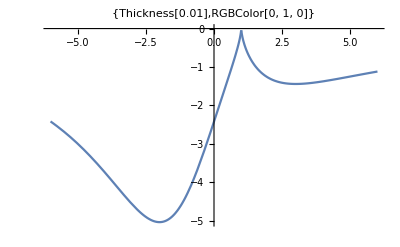

```mathematica
p1=Plot[y[x],{x,−6,6},PlotLabel->{Thickness[0.01],Green}]
```

```mathematica
pt = Table[{x,y[x]},{x,-6,6,1}]
```

{{-6,-4/11 6^(1/3) 7^(2/3)},{-5,-3},{-4,-12/17 5^(2/3) 6^(1/3)},{-3,-2 2^(2/3) 3^(1/3)},{-2,-4 2^(1/3)},{-1,-3 3^(1/3)},{0,-(4 2^(1/3))/3^(2/3)},{1,0},{2,-(12 6^(1/3))/17},{3,-3^(1/3)},{4,-(12 2^(1/3))/11},{5,-6/11 2^(2/3) 3^(1/3)},{6,-4/19 5^(2/3) 6^(1/3)}}

```mathematica
N[pt]//TableForm
```

-6. | -2.41796
-5. | -3.
-4. | -3.75056
-3. | -4.57886
-2. | -5.03968
-1. | -4.32675
0. | -2.42283
1. | 0.
2. | -1.28267
3. | -1.44225
4. | -1.37446
5. | -1.24878
6. | -1.11859

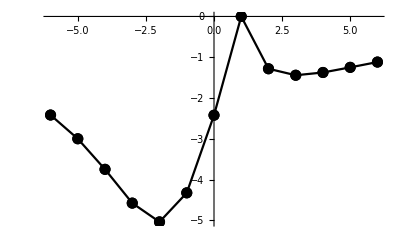

```mathematica
p2 = ListPlot[pt, Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Black}]
```

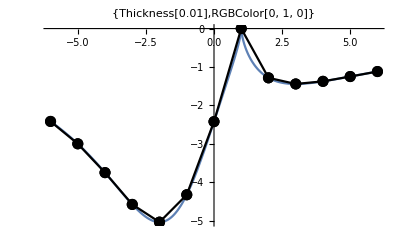

```mathematica
Show[p1,p2]
```

Завдання 2. Побудова графіка полінома.

Використовуючи систему «Mathematica», побудувати графік полінома y(x) . Інтервал для незалежної змінної підібрати самостійно.

```mathematica
Remove[x,y]
```

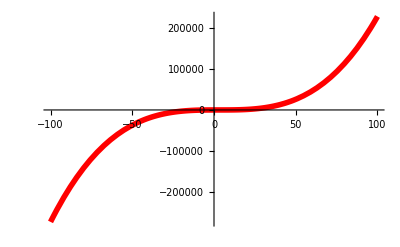

```mathematica
y[x_]=(x^3-9*x^2)/4+6*x-9;
Plot[y[x],{x,-100,100},PlotStyle->{Thickness[0.01],Red}]
```

Завдання 3. Побудова графіка явно заданої функції.

Використовуючи систему «Mathematica», побудувати графік функції y (x). Інтервал незалежної змінної на графіку підібрати самостійно.

```mathematica
Remove[x,y]
```

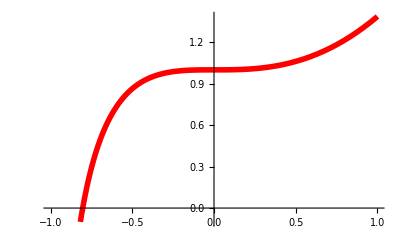

```mathematica
y[x_]=x^2-2*x+2*Log[x+1]+1;
Plot[y[x],{x,-1,1},PlotStyle->{Thickness[0.01],Red}]
```

Завдання 4. Побудова графіка параметричної функції по точках.

Використовуючи систему «Mathematica», побудувати графік функції, яка задана параметрично. Побудувати таблицю координат вузлів ламаної на інтервалі [0,2π]. Побудувати її графік, використовуючи цю таблицю значень. На одному рисунку зобразити графік функції та ламаної.

```mathematica
Remove[x,y,t]
```

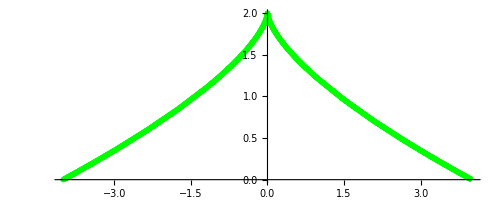

```mathematica
x[t_]=4*Cos[t]^3;
y[t_]=2*Sin[t]^2;
p1 = ParametricPlot[{x[t],y[t]},{t,0,2π},AspectRatio->Automatic, PlotStyle->{Thickness[0.01],Green}]
```

```mathematica
pt=Table[{x[t],y[t]},{t,0,2π, π/4}]
```

{{4,0},{√2,1},{0,2},{-√2,1},{-4,0},{-√2,1},{0,2},{√2,1},{4,0}}

```mathematica
N[pt]//TableForm
```

4. | 0.
1.41421 | 1.
0. | 2.
-1.41421 | 1.
-4. | 0.
-1.41421 | 1.
0. | 2.
1.41421 | 1.
4. | 0.

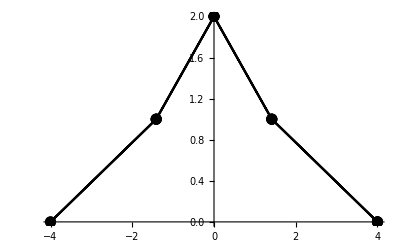

```mathematica
p2=ListPlot[pt,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02], Black}]
```

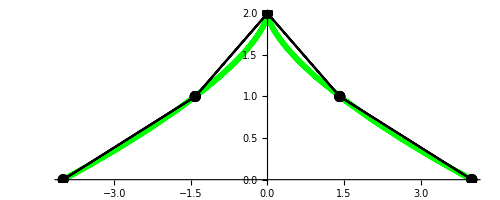

```mathematica
Show[p1,p2]
```

Завдання 5. Побудова графіка функції, яка задана параметрично.

Використовуючи систему «Mathematica», побудувати графік функції, яка задана параметрично.

```mathematica
Remove[x,y,t]
```

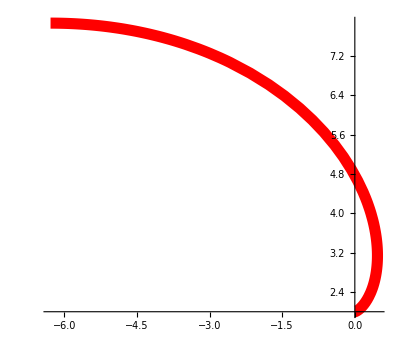

```mathematica
x[t_]=(t^2-2)*Sin[t]+2*t*Cos[t];
y[t_]=(2-t^2)*Cos[t]+2*t*Sin[t];
p1 = ParametricPlot[{x[t],y[t]},{t,0,π},PlotStyle->{Thickness[0.02],Red}]
```

Завдання 6. Побудова графіка функції, яка задана неявно.

Використовуючи систему «Mathematica», побудувати графік функції, яка задана неявно. Діапазони зміни незалежних змінних підібрати самостійно.

```mathematica
Remove[x,y,F]
```

```mathematica
F[x_,y_]=-2*x^2-2*y^2+2*x*y-6*x+6*y+3;
```

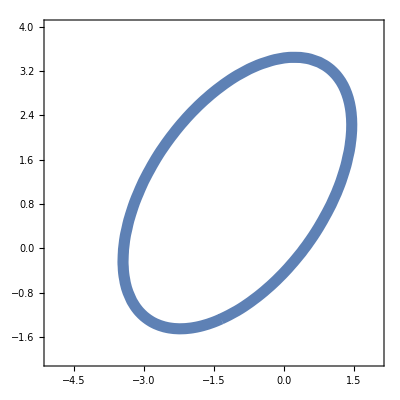

```mathematica
ContourPlot[F[x,y]==0,{x,-5,2},{y, -2,4},ContourStyle->{Thickness[0.02]}]
```

Тема 7. Геометричні побудови.

Завдання 1. Побудова площини по трьом точкам.

```mathematica
Unprotect[C,D]
```

{}

```mathematica
A = {1,-1,1};
B={-2,0,3};
C={2,1,-1};
p1=ListPointPlot3D[{A,B,C},PlotStyle->{Directive[PointSize[0.03],Red]}];
P = {x,y,z};
Eq=Det[{P-A,B-A,C-A}];
```

```mathematica
Eq==0
```

9-6 x-4 y-7 z==0

```mathematica
p2=ContourPlot3D[Eq==0,{x,-3,3},{y,-2,5},{z,-4,4},Mesh->None,ContourStyle->Opacity[0.5]];
```

```mathematica
Show[p1,p2,PlotRange->All,AspectRatio->Automatic]
```

-Graphics3D-

Завдання 2. Паралелограм в просторі.

У просторі дано плоский паралелограм, координати трьох вершин A, B, C якого відомі. Знайти координати четвертої вершини D, яка протилежна вершині A. Обчислити площу паралелограма. В системі Mathematica побудувати контур паралелограма, та його вершини.

```mathematica
Unprotect[C,D];
```

```mathematica
A = {-1,2,-3};
B={3,4,-6};
C={4,1,1};
AB=B-A;
AC=C-A;
D=A+(AB+AC)
```

{8,3,-2}

```mathematica
p1=Graphics3D[{Thickness[0.01],Line[{A,B,D,C,A}]}];
```

```mathematica
p2=ListPointPlot3D[{A,B,D,C},PlotStyle->{Directive[PointSize[0.03],Red]}];
```

```mathematica
Show[p1,p2]
```

-Graphics3D-

```mathematica
S = Norm[Cross[AB,AC]]
```

√1182

Завдання 3. Обчислення в просторовому трикутнику.

У трикутника з вершинами в точках A, B, C знайти довжину висоти h=|BD| , яка проведена з вершини B на протилежну сторону. Знайти довжину медіани, проведеної із вершини B на протилежну сторону. В системі Mathematica побудувати контур трикутника та його медіану.

```mathematica
Unprotect[C];
A={0,1,-2};
B={3,1,2};
C={-4,1,1};
p1=Graphics3D[{Thickness[0.02],Line[{A,B,C,A}]}]
```

-Graphics3D-

```mathematica
AB=B-A;
AC=C-A;
S=1/2*Norm[Cross[AB,AC]]
```

25/2

```mathematica
Remove[h];
```

```mathematica
LAC=Norm[AC];
Solve[1/2*h*LAC==S,h]
```

{{h→5}}

```mathematica
BA=A-B;
BC=C-B;
BM=(BA+BC)/2
```

{-5,0,-5/2}

```mathematica
Norm[BM]
```

(5 √5)/2

```mathematica
M=B+BM
```

{-2,1,-1/2}

```mathematica
p2=Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{B,M}]}];
```

```mathematica
Show[p1,p2,Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Завдання 4. Пряма і площина у просторі.

Знайти точку перетинання прямої і площини. Використовуючи систему «Mathematica», намалювати пряму, площину і точку їх перетинання.

```mathematica
Remove[x,y,z,t]
```

```mathematica
x[t_]=t+1;
y[t_]=0;
z[t_]=-t-3;
```

```mathematica
rez=Solve[2*x-y+4*z==0/.{x->x[t],y->y[t],z->z[t]},t]
```

{{t→-5}}

```mathematica
t0=t/.rez[[1]]
```

-5

```mathematica
{x0,y0,z0}={x[t0],y[t0],z[t0]}
```

{-4,0,2}

```mathematica
pl=ParametricPlot3D[{x[t],y[t],z[t]},{t,-50,50},PlotStyle->Thickness[0.02]];
pp=ContourPlot3D[2*x-y+4*z==0,{x,-50,50},{y,-50,50},{z,-50,50},Mesh->False];
pt=ListPointPlot3D[{{x0,y0,z0}},PlotStyle->{Directive[PointSize[0.05],Red]}];
Show[pl,pp,pt,PlotRange->All]
```

-Graphics3D-

Тема 8. Анімація. Робота з документами Mathematica.

Завдання 1. Анімація кривої.

Побудувати анімацію руху кривої на заданому відрізку часу.

```mathematica
Remove[x,t]
```

```mathematica
Animate[Plot[Sin[π*x]*Sin[t],{x,0,1},PlotRange->1,PlotLabel->t],{t,0,2π},AnimationRunning->False]
```

Завдання 2. Анімація руху точки вздовж кривої.

Побудувати анімацію руху точки вздовж заданого відрізка параметричної кривої.

```mathematica
Remove[x,y,t]
```

```mathematica
x[t_]=(t^2-2)*Sin[t]+2*t*Cos[t];
y[t_]=(2-t^2)*Cos[t]+2*t*Sin[t];
p1=ParametricPlot[{x[tau],y[tau]},{tau,0,π}];
Animate[p2=Graphics[{Green,Disk[{x[t],y[t]},0.15]}];
Show[p1,p2],{t,0.1,π}]
```

Завдання 3. Оформлення документів в Mathematica.

Тема 9. Обчислення границь та похідних

Завдання 1. Послідовність з раціональним загальним членом.

Використовуючи систему «Mathematica», обчислити границю послідовності та надрукувати вісім початкових членів. Якщо знаменник дробу обертається на 0 при n=1 або n=2 , то починайте генерувати послідовність з більшого значення n, наприклад, n = 3.

```mathematica
Remove[x,n]
```

```mathematica
x[n_]=((1-n)^4-(1+n)^4)/((1+n)^3-(1-n)^3);
Table[x[n],{n,1,8}]
```

{-2,-20/7,-10/3,-68/19,-26/7,-148/39,-50/13,-260/67}

```mathematica
N[Table[x[n],{n,1,8}]]
```

{-2.,-2.85714,-3.33333,-3.57895,-3.71429,-3.79487,-3.84615,-3.8806}

```mathematica
Limit[x[n],n->∞]
```

-4

Завдання 2. Послідовність з ірраціональним загальним членом.

Використовуючи систему «Mathematica», обчислити границю послідовності, надрукувати 8 початкових членів в десятковому вигляді,
побудувати графік перших 50 членів. Вертикальний діапазон графіка підібрати самостійно. Інколи перші члени послідовності сильно відрізняються від
граничного значення. Тоді послідовність можна генерувати, починаючи з 5-го, або більшого за номером члена.

```mathematica
Remove[x,n]
```

```mathematica
x[n_]=((n^2-1)^(1/3)+7*n^3)/((n^12+n+1)^(1/4)-n);
```

```mathematica
N[Table[x[n],{n,1,8}]]
```

{22.1467,9.57137,7.95832,7.50777,7.3157,7.21558,7.15665,7.11901}

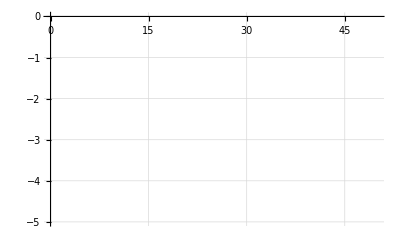

```mathematica
ListPlot[Table[x[n],{n,1,50}],PlotStyle->PointSize[0.02],PlotRange->{-5,0},GridLines->Automatic,Filling->Axis]
```

```mathematica
Limit[x[n],n->∞]
```

7

Завдання 3. Границі різноманітних функцій.

Використовуючи систему «Mathematica», обчислити границю функції. Перевірити, що значення функції наближаються до границі, коли аргумент x прямує до граничного значення x0. Для цього побудувати таблицю значень функції в околі граничного значення x0.

```mathematica
f[x_]=(Tan[x]-Tan[π/3])/(Log[x]-Log[π/3]);
x0=π/3;
y0=Limit[f[x],x->x0];
N[y0]
```

4.18879

```mathematica
f[x0+{0.1,0.01,0.001,0.0001,0.00001,0.000001}]//TableForm
```

5.32601
4.28309
4.19806
4.18972
4.18888
4.1888

Завдання 4. Границя раціональної функції в околі особливої точки.

Використовуючи систему «Mathematica», обчислити границю раціональної функції. Перевірити, що гранична точка є особливою точкою функції. Показати, що значення функції наближаються до граничного, коли аргумент x прямує до граничного значення. Для цього побудувати графік функції в околі особливої точки і зобразити цю точку. Інтервал зміни абсциси в околі особливої точки підібрати самостійно.

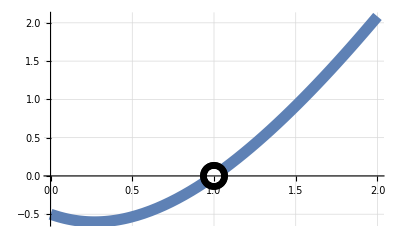

```mathematica
f[x_]=((2*x^2-x-1)^2)/(x^3+2*x^2-x-2);
x0=1;
y0=Limit[f[x],x->x0];
p1=ListPlot[{{x0,y0}},PlotStyle->{Black,PointSize[0.05]}];
p2=ListPlot[{{x0,y0}},PlotStyle->{White,PointSize[0.025]}];
pline=Plot[f[x],{x,x0-1,x0+1},PlotStyle->Thickness[0.02]];
Show[pline,p1,p2,AxesOrigin->{0,0},GridLines->Automatic]
```

Завдання 5. Обчислення похідних.

Використовуючи систему «Mathematica», обчислити похідну y’(x) функції y(x) . Побудувати графік функції y(x) та її похідної y’(x). Обчислити значення похідної в точках x = 0.5,1, 3.0 . При побудові графіків інтервал незалежної змінної підібрати самостійно.

```mathematica
y[x_]=(2*x^2-x-1)/(3 √(2+4*x));
y1[x_]=Simplify[D[y[x],x]]
```

{8,3,-2}[(-1-x+2 x^2)/(3 √(2+4 x)),x]

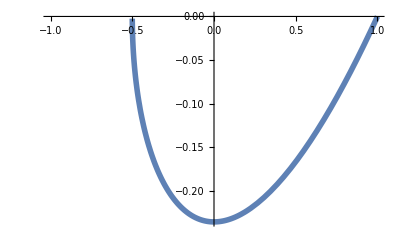

```mathematica
Plot[y[x],{x,1,-1},PlotStyle->Thickness[0.01]]
```

```mathematica
Plot[y1[x],{x,1,-1},PlotStyle->Thickness[0.01]]
```

-Graphics-

```mathematica
y1[{0.5,1,3}]
```

{8,3,-2}[{-0.166667,0,(√14)/3},{0.5,1,3}]

Завдання 6. Похідні виразів, які містять тригонометричні функції.

Використовуючи систему «Mathematica», знайти похідну y’(x) функції y(x) та побудувати її графік. Інтервал абсцис на графіку підібрати самостійно.

```mathematica
y[x_]=Cot[5^(1/3)]-1/8*Cos[4*x]^2/Sin[8*x];
y1[x_]=Simplify[D[y[x],x]]
```

{8,3,-2}[Cot[5^(1/3)]-1/16 Cot[4 x],x]

```mathematica
Plot[y1[x],{x,1,-1},PlotStyle->Thickness[0.01]]
```

-Graphics-

Завдання 7. Похідні вищих порядків.

Використовуючи систему «Mathematica», знайти похідну зазначеного порядку та побудувати її графік. Інтервал незалежної змінної на графіку в кожній задачі підбирати самостійно.

```mathematica
y[x_]=(5*x-1)*Log[x]^2;
```

```mathematica
y3[x_]=Simplify[D[y[x],{x,3}]]
```

{8,3,-2}[(-1+5 x) Log[x]^2,{x,3}]

```mathematica
Plot[y3[x],{x,10,0},PlotStyle->Thickness[0.01]]
```

-Graphics-

Завдання 8. Використання похідних у рівняннях.

Використовуючи систему «Mathematica», показати, що функція y(x) задовольняє рівнянню. В кожному варіанті задана функція та рівняння, якому вона можливо задовольняє.

```mathematica
y[x_]=2+√(1-x^2);
y1[x_]=Simplify[D[y[x],x]]
```

{8,3,-2}[2+√(1-x^2),x]

```mathematica
Simplify[(1-x^2)*y1[x]+x*y[x]==2*x]
```

x √(1-x^2)==(-1+x^2) {8,3,-2}[2+√(1-x^2),x]

Тема 10. Використання диференціального числення.

Завдання 1. Графік дотичної.

Використовуючи систему «Mathematica», скласти рівняння дотичної до кривої в точці з абсцисою х0. Побудувати графіки функції і її дотичної в цій точці. Діапазони зміни x на графіках кривої та дотичної підбирати самостійно.

```mathematica
y[x_]=x^2+8*√x-32;
```

```mathematica
y1[x_]=Simplify[D[y[x],x]];
x0=4;
Y[x_]=y[x0]+y1[x0]*(x-x0)
```

10 (-4+x)

```mathematica
p1=Plot[y[x],{x,6,2},PlotStyle->{Black,Thickness[0.01]}];
```

```mathematica
p2=Plot[Y[x],{x,x0-1,x0+1},PlotStyle->{Red,Thickness[0.01]}];
```

```mathematica
p3=ListPlot[{{x0,y[x0]}},PlotStyle->{Blue,PointSize[0.05]}];
```

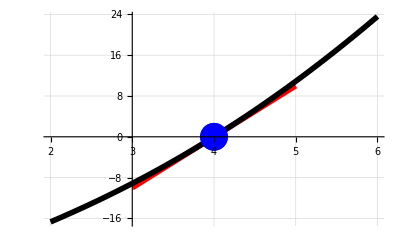

```mathematica
Show[p2,p1,p3,PlotRange->All,GridLines->Automatic]
```

Завдання 2. Дотична та нормаль до параметричної кривої.

Використовуючи систему «Mathematica», в зазначеній точці скласти рівняння дотичної та нормалі до параметрично заданої кривої. Побудувати графіки кривої, зображення точки дотику, а також графіки дотичної і нормалі в цій точці. В кожному варіанті при побудові кривої (графічний об’єкт p1) діапазони зміни параметра t підбирати так, щоб крива в околі точки дотику відображала свої характерні ділянки.

```mathematica
Remove[t]
```

```mathematica
x[t_]=3*t-t^2;
y[t_]=2*t-t^3;
t0=-0.25;
xt=x[t0]+t*x'[t0]
yt=y[t0]+t*y'[t0]
```

-0.8125+3.5 t

-0.484375+1.8125 t

```mathematica
xn[t_]=x[t0]+t*y'[t0]
```

-0.8125+1.8125 t

```mathematica
yn[t_]=y[t0]-t*x'[t0]
```

-0.484375-3.5 t

```mathematica
p1 = ParametricPlot[{x[t],y[t]},{t,-3,3},AspectRatio->Automatic, PlotStyle->Thickness[0.02]];
```

```mathematica
p2=Graphics[{Green,Disk[{x[t0],y[t0]},0.15]}];
```

```mathematica
p3= ParametricPlot[{xt[t],yt[t]},{t,-3,3},PlotStyle->{Red,Thickness[0.02]}];
```

```mathematica
p4= ParametricPlot[{xn[t],yn[t]},{t,-3,3},PlotStyle->{Blue,Thickness[0.01]}];
```

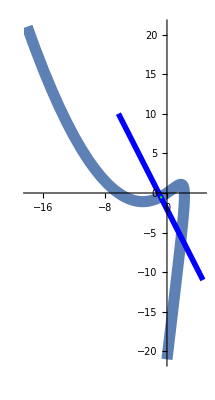

```mathematica
Show[p1,p3,p4,p2,PlotRange->All]
```

Завдання 3. Асимптоти.

Використовуючи систему «Mathematica», знайти асимптоти функції . Побудувати графік функції та всі її похилі і горизонтальні асимптоти. Якщо у функції є вертикальні асимптоти в точках , то ці точки виключити з графіка.

```mathematica
f[x_]=(4*x^2+9)/(4*x+8);
a=Limit[f[x]/x,x->∞]
b=Limit[f[x]-a*x,x->∞]
```

1

-2

```mathematica
Solve[4*x+8==0,x,Reals]
```

{{x→-2}}

```mathematica
Limit[f[x],x->-2]
```

Indeterminate

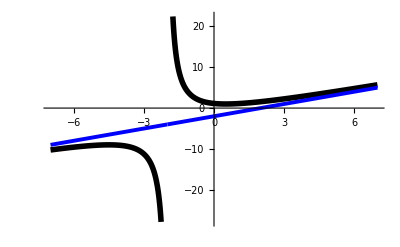

```mathematica
Plot[{f[x],a*x+b},{x,-7,7}, PlotStyle->{{Black,Thickness[0.01]},{Blue,Thickness[0.007]}},Exclusions->{-2}]
```

Завдання 4. Дотична і нормаль до кривої, яка задана неявно.

Використовуючи систему «Mathematica», скласти рівняння дотичної та нормалі до кривої, яка задана неявно. Побудувати графіки кривої, її дотичної та нормалі в точці, яку вибрати самостійно. Інтервали по x і y для зображення кривих в кожному варіанті підбирати окремо.

```mathematica
Remove[x,y,F,x0,y0]
```

```mathematica
F[x_,y_]=14*x^2+24*x*y+21*y^2-4*x+18*y-139;
pc1=ContourPlot[F[x,y]==0,{x,-6,6},{y,-6,6},ContourStyle->{Black,Thickness[0.01]}];
x0=1;
```

```mathematica
rez=N[Solve[F[x0,y]==0,y]]
```

{{y→-3.67261},{y→1.67261}}

```mathematica
y0=rez[[2]][[1,2]]
```

1.67261

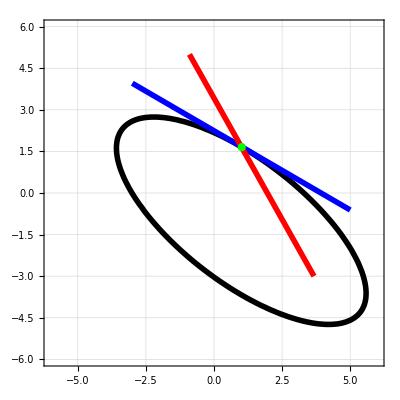

```mathematica
eqT=Derivative[1,0][F][x0,y0](x-x0)+Derivative[0,1][F][x0,y0](y-y0);
eqN=Derivative[1,0][F][x0,y0](y-y0)+Derivative[0,1][F][x0,y0](x-x0);
pc2=ContourPlot[{eqT==0,eqN==0},{x,x0-4,x0+4},{y,x0-4,x0+4},ContourStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}}];
pt=Graphics[{Green,Disk[{x0,y0},0.15]}];
Show[pc1,pc2,pt,AspectRatio->Automatic,GridLines->Automatic]
```

Завдання 5. Найбільше та найменше значення функції на відрізку.

Використовуючи систему «Mathematica», знайти найбільше та найменше значення функції на заданому відрізку. Побудувати графік функції і знайти точки максимуму і мінімуму першим способом. Перевірити отриманий розв’язок, знайшовши і побудувавши точки максимуму і мінімуму другим способом

```mathematica
Remove[x,y];
y[x_]=(2*(x^2+3))/(x^2-2x+5);
a=-3;
b=5;
s=NSolve[y'[x]==0,x,Reals];
{x1,x2}=x/.s
```

{-1.,3.}

```mathematica
{y''[x1],y''[x2]}
```

{0.25,-0.25}

```mathematica
{y[x1],y[x2]}
```

{1.,3.}

```mathematica
{y[a],y[b]}
```

{6/5,14/5}

```mathematica
Xmin=x1;
Ymin=y[x1];
Xmax=x2;
Ymax=y[x2];
```

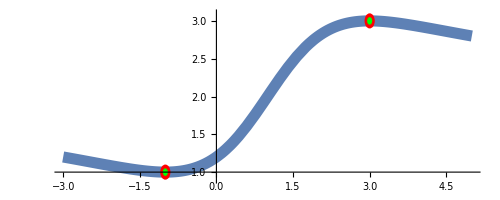

```mathematica
p1 = Plot[y[x],{x,a,b},PlotStyle->Thickness[0.02],AspectRatio->Automatic];
pt=Graphics[{Red,Disk[{Xmin,Ymin},0.1],Disk[{Xmax,Ymax},0.1]}];
mn=Minimize[{y[x],a≤x≤b},x];
{ymin,xmin}={mn[[1]],mn[[2,1,2]]};
mx=Maximize[{y[x],a≤x≤b},x];
{ymax,xmax}={mx[[1]],mx[[2,1,2]]};
pm=Graphics[{Green,Disk[{xmin,ymin},0.05],Disk[{xmax,ymax},0.05]}];
Show[p1,pt,pm,PlotRange->All]
```

Завдання 6. Частинні похідні. Нормаль до поверхні.

Використовуючи систему «Mathematica», обчислити частинні похідні першого і другого порядків функції z(x, y) . Побудувати графік функції і вектор нормалі до її поверхні в заданій точці (x0,y0) . Щоб нормаль до поверхні виглядала як нормаль, підібрати пропорції довжин осей графіка, використовуючи опцію BoxRatios.

```mathematica
Remove[x,y,z]
```

```mathematica
z[x_,y_]=(2*x+3*y)/(10+(x-y)^2);
zx[x_,y_]=Simplify[D[z[x,y],x]]
zy[x_,y_]=Simplify[D[z[x,y],y]]
```

-(2 (-10+x^2+3 x y-4 y^2))/((10+x^2-2 x y+y^2)^2)

(30+7 x^2-4 x y-3 y^2)/((10+x^2-2 x y+y^2)^2)

```mathematica
Simplify[D[z[x,y],{x,2}]]
```

(2 (2 x^3+9 x^2 y-12 x (5+2 y^2)+y (10+13 y^2)))/((10+x^2-2 x y+y^2)^3)

```mathematica
Simplify[D[z[x,y],x,y]]
```

(2 (-7 x^3+6 x^2 y-8 y (-5+y^2)+x (10+9 y^2)))/((10+x^2-2 x y+y^2)^3)

```mathematica
Simplify[D[z[x,y],{y,2}]]
```

(2 (12 x^3-21 x^2 y+3 y (-30+y^2)+x (40+6 y^2)))/((10+x^2-2 x y+y^2)^3)

```mathematica
x0=0.5;
y0=0.5;
P={x0,y0,z[x0,y0]}
```

{0.5,0.5,0.25}

```mathematica
n={zx[x0,y0],zy[x0,y0],-1}
```

{0.2,0.3,-1}

```mathematica
p1=Plot3D[z[x,y],{x,-1,1},{y,-1,1},PlotRange->All,Mesh->None];
p2=Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{P,P+n}]}];
Show[p1,p2,BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Тема 11. Невизначений та визначений інтеграл. Кратні інтеграли.

Завдання 1. Обчислення невизначеного інтеграла.

Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графіки підінтегрального виразу та первісної. На графіках інтервали зміни незалежної змінної підібрати самостійно.

```mathematica
f[x_]=(4*x-2)*Cos[2*x];
F[x_]=Integrate[f[x],x]
```

Cos[2 x]-Sin[2 x]+2 x Sin[2 x]

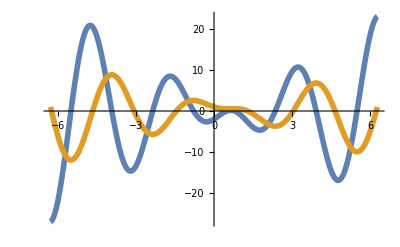

```mathematica
Plot[{f[x],F[x]},{x,-2π,2π},PlotStyle->Thickness[0.01]]
```

Завдання 2. Невизначений інтеграл різноманітних функцій.

Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графік підінтегрального виразу та його первісної. На графіках інтервали зміни незалежної змінної підібрати самостійно.

```mathematica
f[x_]=(x^2+Log[x^2])/x;
g[x_]=∫f[x]ⅆx
```

x^2/2+1/4 Log[x^2]^2

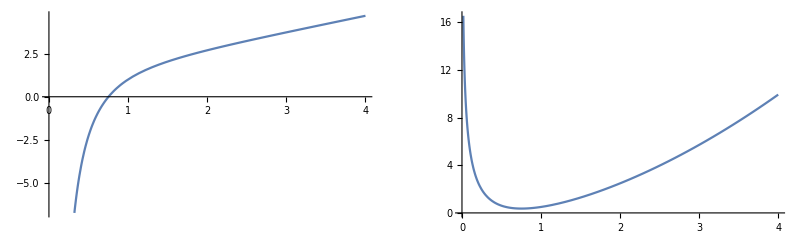

```mathematica
p1=Plot[f[x],{x,0,4}];
p2=Plot[g[x],{x,0,4}];
GraphicsRow[{p1,p2}]
```

Завдання 3. Невизначений інтеграл раціональних функцій.

Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графік підінтегрального виразу та його первісної, виключивши з них особливі точки. На графіках інтервали зміни незалежної змінної підібрати самостійно.

```mathematica
f[x_]=(x^3+6*x^2+14*x+10)/((x+1)*(x+2)^3);
q[x_]=Apart[f[x]]
```

1/(1+x)+2/(2+x)^3

```mathematica
F[x_]=∫q[x]ⅆx
```

-1/(2+x)^2+Log[1+x]

```mathematica
p1=Plot[f[x],{x,-10,10},PlotStyle->Thickness[0.015],Exclusions->{x==-1,x==-2}];
```

```mathematica
p2=Plot[F[x],{x,0,10},PlotStyle->Thickness[0.015]];
```

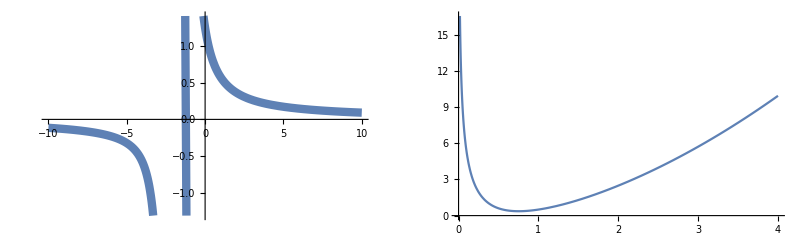

```mathematica
GraphicsRow[{p1,p2}]
```

Завдання 4. Обчислення визначеного інтеграла.

Використовуючи систему «Mathematica», обчислити визначений інтеграл. Побудувати графік підінтегрального виразу і зону, площу якої представляє інтеграл. При побудові кривої інтервал зміни незалежної змінної підбирати ширший за відрізок інтегрування.

```mathematica
f[x_]=(x+2)^2*Cos[x/2];
a=-1;b=1;
s=N[Integrate[f[x],{x,a,b}]]
```

8.28821

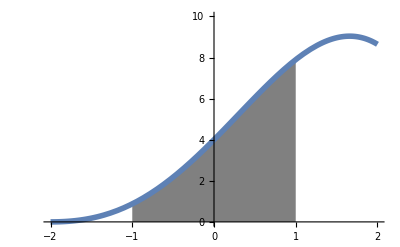

```mathematica
p1=Plot[f[x],{x,a,b},Filling->Axis,FillingStyle->Gray,PlotRange->{0,10}];
p2=Plot[f[x],{x,-2,2},PlotStyle->Thickness[0.01]];
Show[p1,p2,PlotRange->{{-2,2},{0,10}},AxesOrigin->{0,0}]
```

Завдання 5. Визначений інтеграл різноманітних функцій.

Використовуючи систему «Mathematica», обчислити визначений інтеграл. Побудувати графік підінтегрального виразу і область інтегрування. При побудові кривої інтервал зміни незалежної змінної підбирати ширший за відрізок інтегрування.

```mathematica
f[x_]=x^3/(x^2+4);
s=∫_0^2 f[x]ⅆx
```

2-Log[4]

```mathematica
s=N[s]
```

0.613706

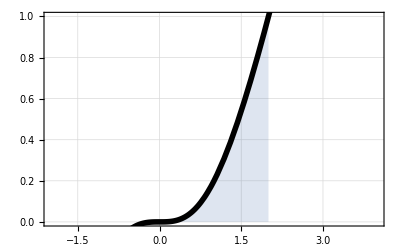

```mathematica
p1=Plot[f[x],{x,0,2},Filling->Axis,AxesOrigin->{0,0}];
p2=Plot[f[x],{x,-2,4},PlotStyle->{Thickness[0.01],Black}];
Show[{p1,p2},PlotRange->{{-2,4},{0,1}},Frame->True,GridLines->Automatic]
```

Завдання 6. Визначений інтеграл від тригонометричних виразів.

Використовуючи систему «Mathematica», обчислити визначений інтеграл. Побудувати графік підінтегрального виразу і область, площу якої представляє інтеграл. При побудові кривої інтервал зміни незалежної змінної підбирати ширший за відрізок інтегрування.

```mathematica
f[x_]=Sin[x/4]^2*Cos[x/4]^6;
s=∫_0^(2*π) f[x]ⅆx
```

(5 π)/64

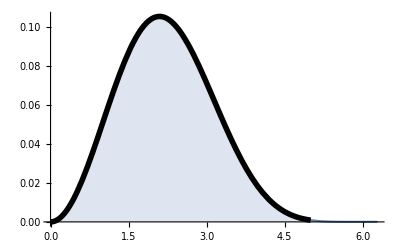

```mathematica
p1=Plot[f[x],{x,0,2*π},Filling->Axis,AxesOrigin->{0,0}];
p2=Plot[f[x],{x,0,5},PlotStyle->{Thickness[0.01],Black}];
Show[{p1,p2},PlotRange->All]
```

Завдання 7. Подвійний інтеграл як повторний.

Використовуючи систему «Mathematica», обчислити подвійний інтеграл по області D як повторний. Графічно зобразити область інтегрування D.

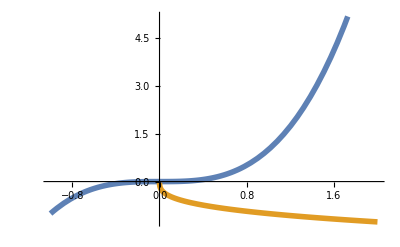

```mathematica
y1[x_]=x^3;
y2[x_]=-x^(1/3);
p1=Plot[{y1[x],y2[x]},{x,-1,2},PlotStyle->Thickness[0.01]]
```

```mathematica
Solve[y1[x]==y2[x],x,Reals]
```

{{x→0}}

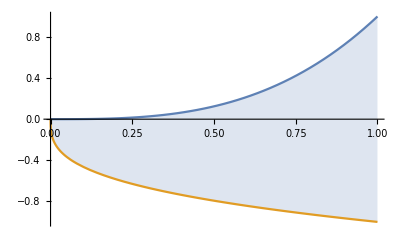

```mathematica
p2=Plot[{y1[x],y2[x]},{x,0,1},Filling->{1->{2}}]
```

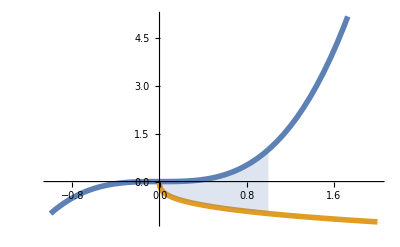

```mathematica
Show[p1,p2]
```

```mathematica
f[x_,y_]=18*x^2*y^2+32*x^3*y^3;
Integrate[f[x,y],{x,0,1},{y,-x^(1/3),x^3}]
```

1

Завдання 8. Обчислення подвійного інтеграла.

З’ясуйте до якого із зазначених вище типів відноситься ваша задача і, враховуючи його, обчисліть подвійний інтеграл по області D як повторний. Графічно зобразіть область D.

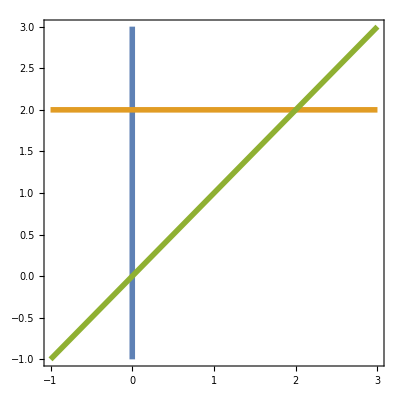

```mathematica
p1=ContourPlot[{x-0==0,y-2==0,y-x==0},{x,-1,3},{y,-1,3},ContourStyle->Thickness[0.01]]
```

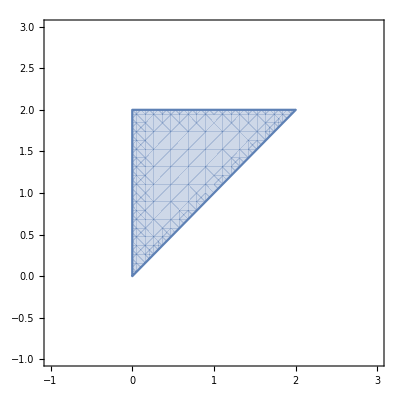

```mathematica
p2=RegionPlot[x<=y<=2&&0<=x<=2,{x,-1,3},{y,-1,3}]
```

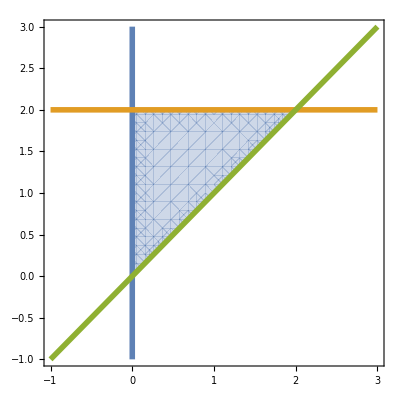

```mathematica
Show[p2,p1]
```

```mathematica
f[x_,y_]=y^2*Exp[-x*y/4];
F=N[Chop[∫_0^2 ∫_x^2 f[x,y]ⅆyⅆx]]
```

2.94304

Тема 12. Застосування інтегрального числення.

Завдання 1. Обчислення площі між двома кривими, які задані явно.

Використовуючи систему «Mathematica», обчислити площу області, яка обмежена графіками функцій між точками їх перетинання. Зобразити графіки функцій та зону, площа якої обчислюється.

```mathematica
y1[x_]=x^2-7*x-2;
y2[x_]=3*x^2+3*x-14;
s=Solve[y1[x]==y2[x],x,Reals]
```

{{x→-6},{x→1}}

```mathematica
x1=x/.s[[1]]
```

-6

```mathematica
x2=x/.s[[2]]
```

1

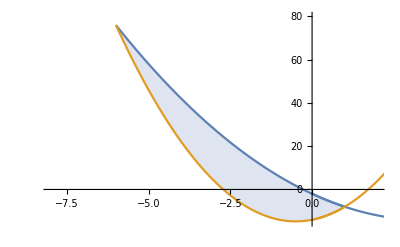

```mathematica
p1=Plot[{y1[x],y2[x]},{x,0,4},PlotRange->{{-8,2},{-15,80}}];
p2=Plot[{y1[x],y2[x]},{x,x1,x2},Filling->{1->{2}}];
Show[p1,p2]
```

```mathematica
Integrate[y1[x]-y2[x],{x,x1,x2}]
```

343/3

Завдання 2. Обчислення довжини кривої, яка задана явно.

Використовуючи систему «Mathematica», обчислити довжину відрізка кривої, рівняння якої задано в явному вигляді. Побудувати графік кривої та криволінійного відрізка, довжина якого обчислюється. Діапазон зміни абсцис графіка підбирати самостійно.

```mathematica
Replace[x]
```

Replace[x]

```mathematica
y[x_]=Log[5/(2*x)];
x1=√3;
x2=√8;
L=∫_x1^x2 √(1+y'[x]^2)ⅆx
```

1+ArcTanh[2]-ArcTanh[3]

```mathematica
N[L]
```

1.20273+0. ⅈ

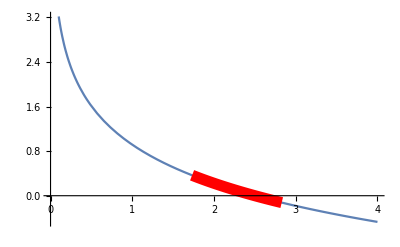

```mathematica
p1=Plot[y[x],{x,0,4}];
p2=Plot[y[x],{x,x1,x2},PlotStyle->{Thickness[0.02],Red}];
Show[p1,p2]
```

Завдання 3. Обчислення довжини параметричної кривої.

Використовуючи систему «Mathematica», обчислити довжину відрізка кривої, яка задана параметричними рівняннями. Побудувати графік криволінійного відрізка, довжина якого обчислюється.

```mathematica
x[t_]=(t^2-2)*Sin[t]+2*t*Cos[t];
y[t_]=(2-t^2)*Cos[t]+2*t*Sin[t];
Tmin=0; Tmax=4*π;
L=Integrate[√(D[x[t],t]^2+D[y[t],t]^2),{t,Tmin,Tmax}]
```

(64 π^3)/3

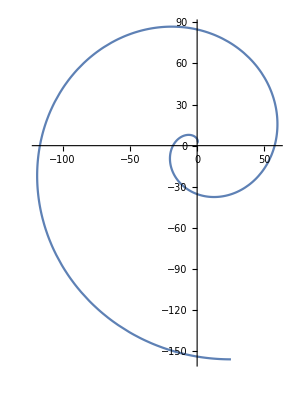

```mathematica
ParametricPlot[{x[t],y[t]},{t,Tmin,Tmax}]
```

Завдання 4. Обчислення маси платівки.

Дано поверхневу густину платівки μ(x, y) і задано область, яку вона займає на площині. Зобразити платівку та знайти її масу.

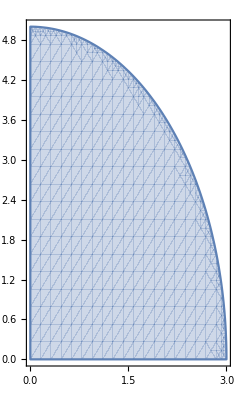

```mathematica
R=x^2/9+y^2/25<=1&&y>=0;
RegionPlot[R,{x,0,3},{y,0,5},AspectRatio->Automatic]
```

```mathematica
mu[x_,y_]=7*x^2*y/18;
M=Integrate[mu[x,y]*Boole[R],{x,0,3},{y,0,5}]
```

35/2

Завдання 5. Обчислення об’єму тіла.

Знайти об’єм тіла, яке задано нерівностями. Побудувати зображення тіла.

```mathematica
R = (4<=x^2+y^2+z^2<=36)&&(0<=y<=x/√3)&&(-√((x^2+y^2)/63)<=z);
RegionPlot3D[R,{x,0,6},{y,0,3},{z,0,6},PlotPoints->100,Boxed->False,AxesOrigin->{0,0,0},Mesh->None]
```

-Graphics3D-

```mathematica
Chop[NIntegrate[Boole[R],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]]
```

40.8407